```mathematica
x1[t_] :=(Tanh[(t-0.05)/0.02]+1)/2((Tanh[(t-0.25)/0.15]-1)/(-2/0.8)+0.2)
```

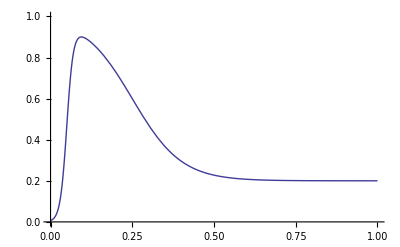

```mathematica
Plot[x1[t],{t,0,1}, PlotRange->{{0,1},{0,1}}]
```

```mathematica
x2[t_] :=(Tanh[((Log10[t]/10+1)-0.1)/0.02]+1)/2((Tanh[((Log10[t]/10+1)-0.25)/0.15]-1)/(-2/0.8)+0.2)
```

```mathematica
x2[t]//Simplify
```

-0.2 (-1.5+1. Tanh[5.+0.28953 Log[t]]) (1.+Tanh[45.+2.17147 Log[t]])

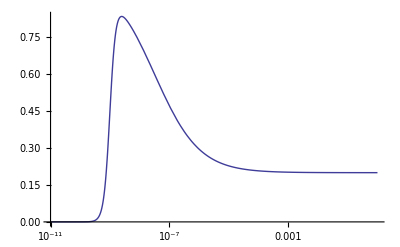

```mathematica
LogLinearPlot[x2[t],{t,0.00000000001,1}]
```

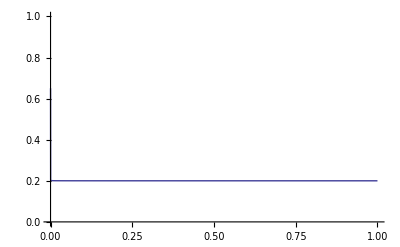

```mathematica
Plot[x2[t],{t,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
x3[t_]:=-0.2(-1.5+ Tanh[(1.3+0.08 Log[t])/0.3]) (1+Tanh[(0.8+0.04 Log[t])/0.02])
```

```mathematica
x3[t]//FullSimplify
```

-0.2 (-1.5+Tanh[4.33333+0.266667 Log[t]]) (1+Tanh[40.+2. Log[t]])

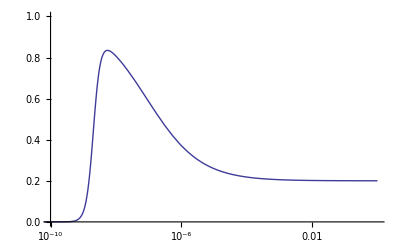

```mathematica
LogLinearPlot[x3[t],{t,0.00000000001,1},PlotRange->{{0.0000000001,1},{0,1}}]
```

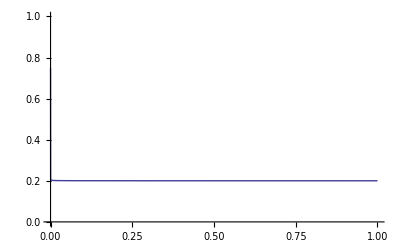

```mathematica
Plot[x3[t],{t,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
x4[t_]:=-0.2(-1.5+ (Exp[(1.3+0.08 Log[t])/0.3]-Exp[-(1.3+0.08 Log[t])/0.3])/(Exp[(1.3+0.08 Log[t])/0.3]+Exp[-(1.3+0.08 Log[t])/0.3]))(1+(Exp[(0.8+0.04 Log[t])/0.02]-Exp[-(0.8+0.04 Log[t])/0.02])/(Exp[(0.8+0.04 Log[t])/0.02]+Exp[-(0.8+0.04 Log[t])/0.02]))
```

```mathematica
x4[t]//FullSimplify
```

(0.000172232 t^4.+0.2 t^4.53333)/((0.000172232+1. t^0.533333) (1.80485×10^-35+1. t^4.))

```mathematica
x5[t_]:=1.4(0.0001 t^4+0.1 t^(9/2))/((0.0001+t^(1/2)) (10^-36+ t^4))
```

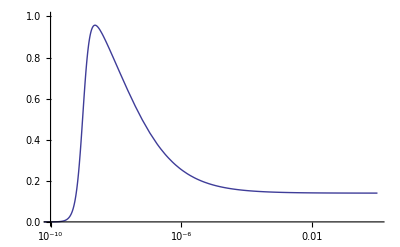

```mathematica
LogLinearPlot[x5[t],{t,0.00000000001,1},PlotRange->{{0.0000000001,1},{0,1}}]
```

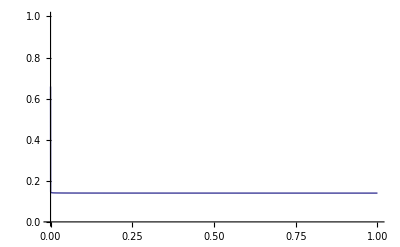

```mathematica
Plot[x5[t],{t,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
x6[t_]:=a(b t^4+c t^(9/2))/((b+t^(1/2)) (d+ t^4))
```

```mathematica
x6[t]
```

(a (b t^4+c t^(9/2)))/((b+√t) (d+t^4))

```mathematica
CForm[x6[t]]/. {Power -> pow}
```

a*(b*pow(t,4) + c*pow(t,4.5))*pow(b + pow(t,0.5),-1)*pow(d + pow(t,4),-1)

```mathematica
D[x6[t],t]//Simplify
```

(a t^3 (8 b^2 d+8 c d t+b √t ((7+9 c) d+(-1+c) t^4)))/(2 (b+√t)^2 (d+t^4)^2)

```mathematica
CForm[Simplify[D[x6[t],t]]] /. {Power -> pow}
```

(a*pow(t,3)*(8*c*d*t + 8*d*pow(b,2) + 
       b*pow(t,0.5)*((7 + 9*c)*d + (-1 + c)*pow(t,4)))*pow(b + pow(t,0.5),-2)*
     pow(d + pow(t,4),-2))/2.

```mathematica
x6[t]//TeXForm
```

\frac{a \left(b t^4+c t^{9/2}\right)}{\left(b+\sqrt{t}\right) \left(d+t^4\right)}

```mathematica
Simplify[D[x6[t],t]]//TeXForm
```

\frac{a t^3 \left(8 b^2 d+b \sqrt{t} \left((9 c+7) d+(c-1) t^4\right)+8 c d
   t\right)}{2 \left(b+\sqrt{t}\right)^2 \left(d+t^4\right)^2}